```mathematica
K[n_]:=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
P[n_,k_]:=P[n,k]=Sum[ K[j]P[Floor[n/j],k-1],{j,2,n}];P[n_,0]:=1
D2[n_,k_]:=D2[n,k]=Sum[D2[Floor[n/j],k-1],{j,2,n}];D2[n_,0]:=1
DD[n_,z_]:=Sum[FactorialPower[z,a]/a! D2[n,a],{a,0,Log[2,n]}]
P[n_,k_,s_]:=P[n,k,s]=Sum[ j^-s K[j]P[Floor[n/j],k-1,s],{j,2,n}];P[n_,0,s_]:=1
DDa[n_, z_] := Sum[ z^k/k! P[n,k],{k,0,Log[2,n]}]
DDa[n_, z_,s_] := Sum[ z^k/k! P[n,k,s],{k,0,Log[2,n]}]
DDa2[n_, z_] := Sum[ z^k/k! P[n,k]/z,{k,0,Log[2,n]}]
Dhyp[n_,k_,a_]:=Dhyp[n,k,a]=Sum[Binomial[k,j] Dhyp[Floor[n/(m^(k-j))],j,m+1],{m,a,n^(1/k)},{j,0,k-1}]
Dhyp[n_,1,a_]:=Floor[n]-a+1;Dhyp[n_,0,a_]:=1
bins[ z_, a_] := Product[ (z-k),{k,0,a-1}]/a!
DDD[n_,z_]:=Expand[Sum[bins[z,a] Dhyp[n,a,2],{a,0,Log[2,n]}]]
lin[n_] := Sum[ (-1)^(k+1)/k Dhyp[n,k,2],{k,1,Log[2,n]}]

df[ n_, x_, k_, l_] := Sum[ df[n/j,x,k,l-1],{j,1,x}]
df[n_, x_, k_, 0 ] := Dhyp[ n,k,1]
df2[n_, k_, x_] := x^-k Sum[ (-1)^j Binomial[k,j]df[ n x^k, x, k-j, j],{j,0,k}]
```

```mathematica
di[ n_, x_, k_, l_] := Sum[ di[n/j,x,k,l-1],{j,2,x}]
di[n_, x_, k_, 0 ] := Dhyp[ n,k,2]
di2[n_, k_, x_] := x^-k Sum[ (-1)^j Binomial[k,j]di[ n x^k, x, k-j, j],{j,0,k}]
```

```mathematica
di[100,2,2,0]
```

283

```mathematica
df2[100,3,40]
```

5483447/8000

```mathematica
di2[100,3,40]
```

5483447/8000

```mathematica
Gamma[3,-Log[100]]/Gamma[3]
```

1/2 Gamma[3,-Log[100]]

```mathematica
40^-3Dhyp[ 100 40^3, 3, 40+1]
```

5483447/8000

```mathematica
Binomial[3,2]
```

3

```mathematica
Binomial[2,1]
```

2

```mathematica
f[ x_] := Sum[ 1, {j,2,x},{k,2,x},{m,2,x}]
```

```mathematica
Table[ f[n]-f[(n-1)],{n,2,40}]//TableForm
```

1
7
19
37
61
91
127
169
217
271
331
397
469
547
631
721
817
919
1027
1141
1261
1387
1519
1657
1801
1951
2107
2269
2437
2611
2791
2977
3169
3367
3571
3781
3997
4219
4447

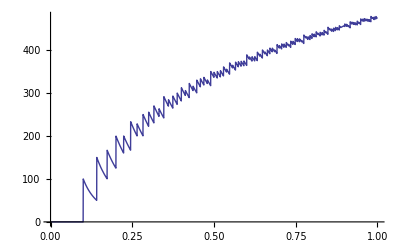

```mathematica
Plot[df2[100,2,n],{n,0,1}]
```

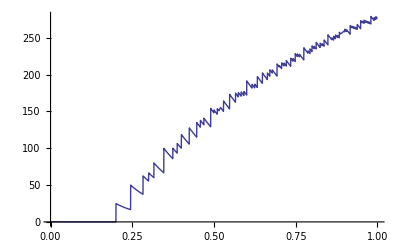

```mathematica
Plot[di2[100,2,n],{n,0,1}]
```

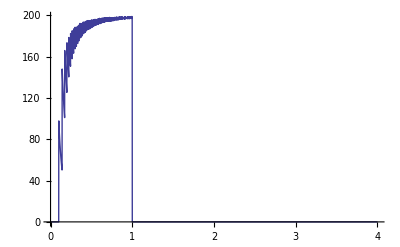

```mathematica
Plot[df2[100,2,n]-di2[100,2,n],{n,0,4}]
```

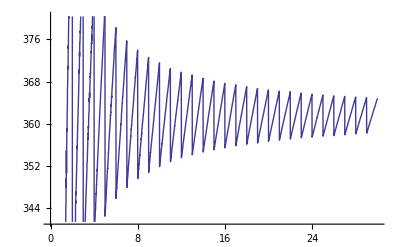

```mathematica
Plot[di2[100,2,n],{n,0,30}]
```

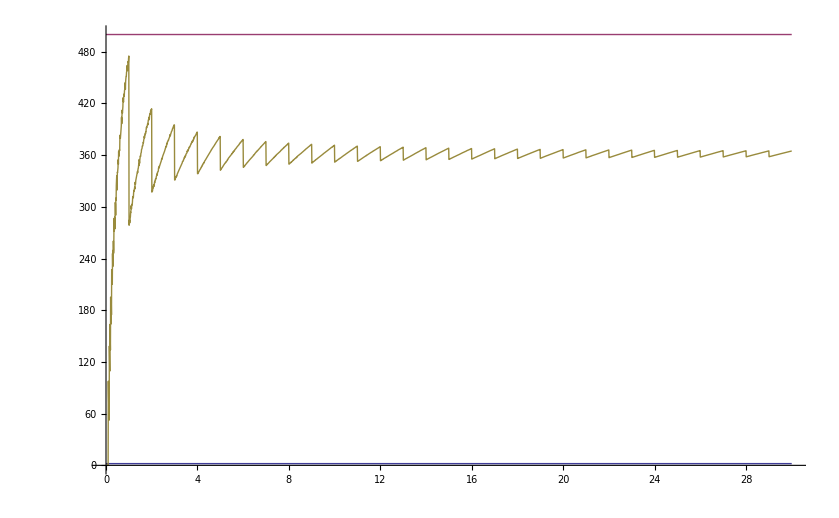

```mathematica
Plot[{2,500,df2[100,2,n]},{n,0,30}]
```

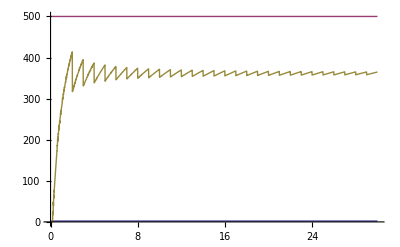

```mathematica
Plot[{2,500,di2[100,2,n]},{n,0,30}]
```

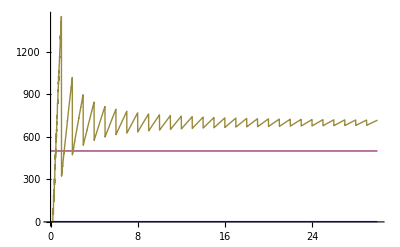

```mathematica
Plot[{2,500,df2[100,3,n]},{n,0,30}]
```

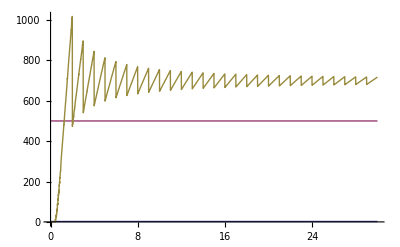

```mathematica
Plot[{2,500,di2[100,3,n]},{n,0,30}]
```

```mathematica
Binomial[3,-1]
```

0

```mathematica
Binomial[0,-1]
```

0

```mathematica
dg[ n_, x_, k_, l_] := Sum[ dg[n/j,x,k,l-1],{j,1,x}]
dg[n_, x_, k_, 0 ] := DDD[ n,k]
dg2[n_, k_, x_] := x^-k Sum[ (-1)^j Binomial[k,j]dg[ n x^k, x, k-j, j],{j,0,6k}]
```

```mathematica
dg2[100,2.5,5]
```

$Aborted